```mathematica
(* Notebook for the resonant tunnelling of a massive particle through a double potential barrier. *)
```

0

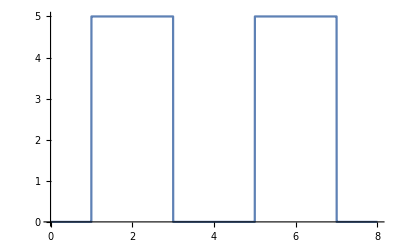

```mathematica
ClearAll["Global`*"];
(* Start by defining the potential. *)
v=5; (* Magnitude of the potential. *)
a=2; (* Width the of barriers. *)
d=1; (* Distance of first barrier from origin. *)
w=2.0; (* Separation of barriers. *)
V[r_]:=Piecewise[{{v,d<r<(d+a)},{v,(d+w+a)<r<(d+w+2a)}},0];
V[9]
Plot[V[r],{r,0,8},Exclusions->None]
```

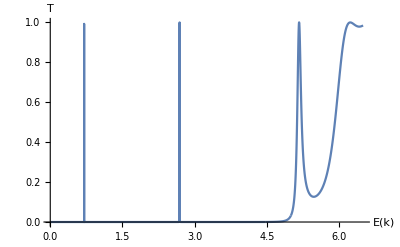

```mathematica
(* Define relevant constants and useful groups of function and substitute into the formula for the transmission coefficient. *)
hbar=1; (* constant, hbar, usually set to 1 for convenience. *)
M=1; (* mass, usually set to 1 for convenience. *)
k[ϵ_]:=√((2M ϵ)/hbar^2); (* wave vector in regions of 0 potential *)
kbar[ϵ_]:=√((2 M (v-ϵ))/hbar^2) ; (* wave vector inside the barrier. *)
H[ϵ_]:=2 √(ϵ(v-ϵ))Cosh[kbar[ϵ]a] Cos[k[ϵ]w]-(2ϵ-v)Sinh[kbar[ϵ]a]Sin[k[ϵ]w];
T[ϵ_]:=(1+(v^2(H[ϵ])^2(Sinh[kbar[ϵ]a])^2)/(4 ϵ^2(v-ϵ)^2))^-1;
Plot[T[ϵ],{ϵ,0,6.5},PlotRange->All,PlotPoints->10000,AxesLabel->{"E(k)","T",FontSize->24}]
```

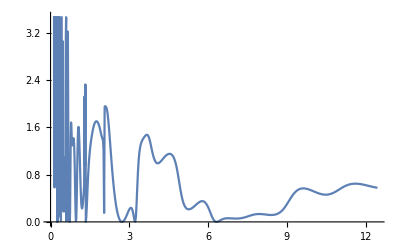

```mathematica
(* Calculate the scattering length shift λ(k) *)
κ=1; (* alternative wave vector variable (k) so as not to interfere with section 1 *)
m=0;
λ={}; (* list for storing the scattering length λ for each k *)
ν={}; (* list for storing k value corresponding to the element of λ(k) *)
κlimit=5; rlimit=10;
iterations=5; (* number of iterations to conduct *)


For[κ=0.5,κ<κlimit,κ+=0.01,
Monitor[
For[i=0,i<iterations,i++,
δtemp=NDSolveValue[{δ'[r]==-π/2 r V[r](BesselJ[m,κ r]Cos[δ[r]]-BesselY[m,κ r]Sin[δ[r]])^2,δ[0.1]==0},δ,{r,0.1,rlimit}];
δ[r]=δtemp[r];],{κ,i,δtemp[rlimit]}]
AppendTo[λ,4/κ(Sin[δtemp[rlimit]])^2]
AppendTo[ν,κ^2/2]
Clear[δtemp]]
λκ=Transpose[{ν,λ}];
ListLinePlot[λκ]
```

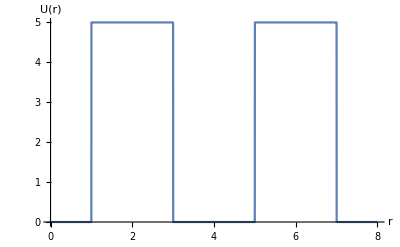

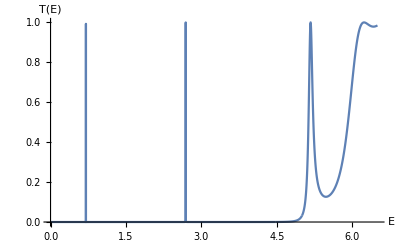

```mathematica
Plot[V[r],{r,0,8},Exclusions->None,TicksStyle->Directive[Black, FontSize->48],AxesLabel->{r,"U(r)"},LabelStyle->Directive[Black,FontSize->48]]

Plot[T[ϵ],{ϵ,0,6.5},PlotRange->All,PlotPoints->10000,TicksStyle->Directive[Black, FontSize->48],AxesLabel->{"E","T(E)"},LabelStyle->Directive[Black,FontSize->48]]
```

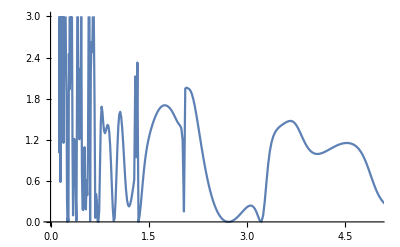

```mathematica
ListLinePlot[λκ,PlotRange->{{0,5},{0,3}}]
```